#### Wulffnator

code for wulf construction.

```mathematica
(*define the function here, periodic over π/2 is taken care of*)
f[θ_] := 2(Abs[0.1Cos[3θ]]+1)
tan[ϕ_] :=  -Cos[ϕ]/Sin[ϕ]
```

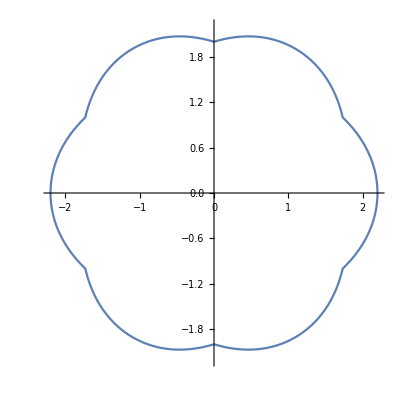

```mathematica
Show[
{ PolarPlot[f[θ],{θ,0, π/2}],
PolarPlot[f[π-θ],{θ,π/2, π}],
PolarPlot[f[θ-π],{θ,π, 3 π/2}],
PolarPlot[f[2π -θ],{θ,3 π/2, 2π}]},PlotRange-> {{-2.2,2.2},{-2.2,2.2}}]
```

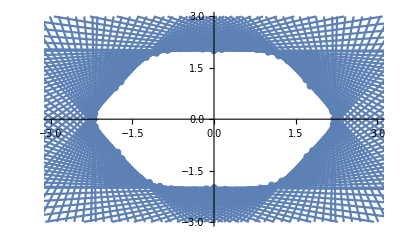

```mathematica
Show[ListPlot[Table[{f[ϕ]Cos[ϕ],f[ϕ]Sin[ϕ] }  ,{ϕ, 0+0.001, π/2-0.001, 0.1}] ,PlotRange->{{-3.,3},{-3,3}}],
	Table[Plot[tan[ϕ]x + ( f[ϕ]Sin[ϕ] -tan[ϕ]f[ϕ]Cos[ϕ] )  ,{x,-10,10},PlotRange->{{-3.,3},{-3,3}}],{ϕ, 0+0.01, π/2-0.01, 0.05}],

ListPlot[Table[{f[π-ϕ]Cos[ϕ],f[π-ϕ]Sin[ϕ] }  ,{ϕ, π/2+0.001, π-0.001, 0.1}] ,PlotRange->{{-3.,3},{-3,3}}],
	Table[Plot[-tan[π-ϕ]x + ( f[π-ϕ]Sin[ϕ] +tan[π-ϕ]f[π-ϕ]Cos[ϕ] )  ,{x,-10,10},PlotRange->{{-3.,3},{-3,3}}],{ϕ, π/2+0.001, π-0.001, 0.05}],

ListPlot[Table[{f[ϕ - π ]Cos[ ϕ ],f[ϕ - π]Sin[ϕ ] }  ,{ϕ, π+0.001, (3π)/2-0.001, 0.1}] ,PlotRange->{{-3.,3},{-3,3}}],
	Table[Plot[tan[ϕ - π]x + ( f[ϕ - π]Sin[ϕ ] -tan[ϕ ]f[ϕ - π]Cos[ϕ] )  ,{x,-10,10},PlotRange->{{-3.,3},{-3,3}}],{ϕ, π+0.01, (3π)/2-0.01, 0.05}],

ListPlot[Table[{f[2π-ϕ]Cos[ϕ],f[2π-ϕ]Sin[ϕ] }  ,{ϕ, (3π)/2+0.001, 2π-0.001, 0.1}] ,PlotRange->{{-3.,3},{-3,3}}],
	Table[Plot[-tan[2π-ϕ]x + ( f[2π-ϕ]Sin[ϕ] +tan[2π-ϕ]f[2π-ϕ]Cos[ϕ] )  ,{x,-10,10},PlotRange->{{-3.,3},{-3,3}}],{ϕ, (3π)/2+0.001, 2π-0.001, 0.05}]
]
```